# Iteration 3: Recovery of Turned Zombies

Building on the previous iteration, the turned zombies recover into humans.

The system is governed by the following equations.
H’ == - βZ H Z + δT T
Z’ == βZ H Z - δZT T Z - δZH H Z
T’ == βT R - δT T
 R’ ==  δZH H Z + δZT T Z - βT R

```mathematica
Manipulate[
 Module[
  {
   eqns, sol, H, Z, T, R, t, Hfunc, Zfunc, Tfunc, Rfunc, fixedPoints, 
   phasePlotHZ, phasePlotZT, jMatrix, parameterSpace,
   detJ, finalDetJ, traceJ, finalTraceJ
  },
  
  (* Define the differential equations *)
  eqns = {
    H'[t] == - βZ H[t] Z[t] + δT T[t],
    Z'[t] == βZ H[t] Z[t] - δZT T[t] Z[t] - δZH H[t] Z[t],
    T'[t] == βT R[t] - δT T[t],
    R'[t] ==  δZH H[t] Z[t] + δZT T[t] Z[t] - βT R[t]
  };
  
  jMatrix = {
   {-βZ Z, -βZ H, δT, 0},
   {(βZ - δZH)Z, (βZ - δZT)H, -δZT Z, 0},
   {0, 0, - δT, βT},
   {δZH Z, δZT H+ δZH H - δZT T, -δZT Z, - βT}
};
  
  parameterSpace = ParametricPlot[{{d,0},{0,t},{t^2/4,t}},{d,-10,10},{t,-10,10},PlotRange->{{-10,10},{-10,10}}];
  
  (* Solve the equations numerically *)
  sol = NDSolve[
    {eqns, 
     H[0] == H0, 
     Z[0] == Z0,
     T[0] == T0,
     R[0] == R0
    }, 
    {H, Z, T, R}, 
    {t, 0, tmax}
  ];
  
  (* Extract solution functions *)
  Hfunc = H /. sol[[1]];
  Zfunc = Z /. sol[[1]];
  Tfunc = T /. sol[[1]];
  Rfunc = R /. sol[[1]];
  
  traceJ = Tr[jMatrix];
  detJ = Det[jMatrix];
  finalTraceJ = traceJ /. {H -> (H[tmax] /. sol[[1]]), Z -> (Z[tmax] /. sol[[1]]), R -> (R[tmax] /. sol[[1]]), βZ -> βZ, δZ -> δZ };
  finalDetJ = detJ /. {H -> (H[tmax] /. sol[[1]]), Z -> (Z[tmax] /. sol[[1]]), R -> (R[tmax] /. sol[[1]]), βZ -> βZ, δZ -> δZ };
  
  
  
  (* Generate phase space stream plot *)
  phasePlotHZ = 
   StreamPlot[
    Evaluate[{
    
      - βZ H Z + δT T, 
      βZ H Z - δZT T Z - δZH H Z
    } /. {T -> Tfunc[tmax]}],
    {H, 0, 1}, {Z, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    AxesLabel -> {"H (Humans)", "Z (Zombies)"},
    Frame -> True,
    FrameLabel -> {"H (Humans)", "Z (Zombies)"}
   ];
   phasePlotZT = 
   StreamPlot[
    Evaluate[{ 
      βZ H Z - δZT T Z - δZH H Z,
      βT R - δT T
    } /. {R -> Rfunc[tmax], H -> Hfunc[tmax]}],
    {Z, 0, 1}, {T, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    AxesLabel -> {"Z (Zombies)", "Turned (T)"},
    Frame -> True,
    FrameLabel -> {"Z (Zombies)", "Turned (T)"}
   ];
  
  (* Display the results *)
  Column[{
    Plot[
     {Hfunc[t], Zfunc[t], Tfunc[t], Rfunc[t]},
     {t, 0, tmax},
     PlotRange -> All,
     PlotLegends -> {"Humans (H)", "Zombies (Z)", "Turned (T)", "Removed (R)"},
     PlotStyle -> {{Blue, Thick}, {Red, Thick}, {Green, Thick}, {Purple, Thick}},
     AxesLabel -> {"Time (t)", "Population"},
     Frame -> True,
     FrameLabel -> {"Time (t)", "Population Fractions"}
    ],
    phasePlotHZ,
    phasePlotZT
   }]
 ],
 
 (* Sliders for parameters and initial conditions *)
 {{βZ, 0.0095, "Zombification rate H to Z (beta_Z)"}, 0, 1, 0.001},
 {{δZT, 0.013, "Zombie removal rate by turned zombies (delta_ZT)"}, 0, 1, 0.001},
 {{δZH, 0.006, "Zombie removal rate by humans (delta_ZH)"}, 0, 1, 0.001},
 {{βT, 0.003, "Resurrection rate R to T (beta_T)"}, 0, 1, 0.001},
 {{δT, 0.002, "Turned recovery rate T to H (delta_T)"}, 0, 1, 0.001},
 {{H0, 500, "Initial humans (H0)"}, 1, 5000, 1},
 {{Z0, 100, "Initial zombies (Z0)"}, 1, 5000, 1},
 {{T0, 10, "Initial turned (T0)"}, 1, 5000, 1},
 {{R0, 0, "Initial removed (R0)"}, 0, 5000, 1},
 {{tmax, 100000, "Simulation time"}, 10, 1000000, 1}
]
```

NDSolve::ndsz: At t$636241 == 1283.35, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t$640860 == 1283.35, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

## Non-Dimensionalisation

The system can be non-dimensionalised by considering dimensionless time to be governed by the zombification rate (β_Z) and the scaling the population using the initial human population (H_0).

```mathematica
Manipulate[
 Module[
  {
   eqns, sol, H, Z, T, R, t, Hfunc, Zfunc, Tfunc, Rfunc, fixedPoints, 
   phasePlotHZ, phasePlotHT, phasePlotZT, jMatrix, parameterSpace,
   detJ, finalDetJ, traceJ, finalTraceJ
  },
  
  (* Define the differential equations *)
  eqns = {
    H'[t] == - H[t] Z[t]+δT T[t],
    Z'[t] == H[t] Z[t] - δZT T[t] Z[t] - δZH H[t] Z[t],
    T'[t] == βT R[t] - δT T[t],
    R'[t] ==  δZH H[t] Z[t] + δZT T[t] Z[t] - βT R[t]
  };
  
  jMatrix = {
   {- Z, - H, δT, 0},
   {(1 - δZH)Z, (1 - δZH)H-δZT T, -δZT Z, 0},
   {0, 0, - δT, βT},
   {δZH Z, δZT Z+ δZH H, δZT Z, - βT}
};
  
  parameterSpace = ParametricPlot[{{d,0},{0,t},{t^2/4,t}},{d,-10,10},{t,-10,10},PlotRange->{{-10,10},{-10,10}}];
  
  (* Solve the equations numerically *)
  sol = NDSolve[
    {eqns, 
     H[0] == H0/H0, 
     Z[0] == Z0/H0,
     T[0] == T0/H0,
     R[0] == R0/H0
    }, 
    {H, Z, T, R}, 
    {t, 0, tmax}
  ];
  
  (* Extract solution functions *)
  Hfunc = H /. sol[[1]];
  Zfunc = Z /. sol[[1]];
  Tfunc = T /. sol[[1]];
  Rfunc = R /. sol[[1]];
  
  traceJ = Tr[jMatrix];
  detJ = Det[jMatrix];
  finalTraceJ = traceJ /. {H -> (H[tmax] /. sol[[1]]), Z -> (Z[tmax] /. sol[[1]]), T -> (T[tmax] /. sol[[1]]), R -> (R[tmax] /. sol[[1]]), βT -> βT, δZH -> δZH, δZT -> δZT, δT -> δT };
  finalDetJ = detJ /. {H -> (H[tmax] /. sol[[1]]), Z -> (Z[tmax] /. sol[[1]]), T -> (T[tmax] /. sol[[1]]), R -> (R[tmax] /. sol[[1]]), βT -> βT, δZH -> δZH, δZT -> δZT, δT -> δT };
  
  
  
  (* Generate phase space stream plot *)
  phasePlotHZ = 
   StreamPlot[
    Evaluate[{
    
      - H Z + δT T, 
      H Z - δZT T Z - δZH H Z
    } /. {T -> Tfunc[tmax]}],
    {H, 0, 1}, {Z, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    AxesLabel -> {"H (Humans)", "Z (Zombies)"},
    Frame -> True,
    FrameLabel -> {"H (Humans)", "Z (Zombies)"}
   ];
   phasePlotHT = 
   StreamPlot[
    Evaluate[{
      - H Z + δT T, 
      βT R - δT T
    } /. {R -> Rfunc[tmax], Z -> Zfunc[tmax]}],
    {H, 0, 1}, {T, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    AxesLabel -> {"H (Humans)", "T (Turned)"},
    Frame -> True,
    FrameLabel -> {"H (Humans)", "T (Turned)"}
   ];
   phasePlotZT = 
   StreamPlot[
    Evaluate[{ 
       H Z - δZT T Z - δZH H Z,
      βT R - δT T
    } /. {R -> Rfunc[tmax], H -> Hfunc[tmax]}],
    {Z, 0, 1}, {T, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    AxesLabel -> {"Z (Zombies)", "Turned (T)"},
    Frame -> True,
    FrameLabel -> {"Z (Zombies)", "Turned (T)"}
   ];
  
  (* Display the results *)
  Column[{
    Plot[
     {Hfunc[t], Zfunc[t], Tfunc[t], Rfunc[t]},
     {t, 0, tmax},
     PlotRange -> All,
     PlotLegends -> {"Humans (H)", "Zombies (Z)", "Turned (T)", "Removed (R)"},
     PlotStyle -> {{Blue, Thick}, {Red, Thick}, {Green, Thick}, {Purple, Thick}},
     AxesLabel -> {"Time (t)", "Population"},
     Frame -> True,
     FrameLabel -> {"Time (t)", "Population Fractions"}
    ],
    phasePlotHZ,
    phasePlotHT,
    phasePlotZT,
    Show[
		parameterSpace,
		ListPlot[{{finalDetJ,finalTraceJ}},PlotStyle->PointSize[Large]]
	]
   }]
 ],
 
 (* Sliders for parameters and initial conditions *)
 {{δZT, 1.36, "Zombie removal rate by turned zombies (delta_ZT)"}, 0, 5, 0.001},
 {{δZH, 0.631, "Zombie removal rate by humans (delta_ZH)"}, 0, 5, 0.001},
 {{βT, 0.31, "Resurrection rate R to T (beta_T)"}, 0, 5, 0.001},
 {{δT, 0.2, "Turned removal rate (delta_T)"}, 0, 5, 0.001},
 {{H0, 500, "Initial humans (H0)"}, 1, 5000, 1},
 {{Z0, 50, "Initial zombies (Z0)"}, 1, 5000, 1},
 {{T0, 50, "Initial turned (T0)"}, 1, 5000, 1},
 {{R0, 0, "Initial removed (R0)"}, 0, 5000, 1},
 {{tmax, 200, "Simulation time"}, 10, 1000000, 1}
]
```

```mathematica
(* Solve the steady-state equations for fixed points *)
fixedPoints = NSolve[
  {
    - H Z+ δT T ==0,
    H Z - δZT T Z - δZH H Z ==0,
    βT R - δT T ==0,
    δZH H Z + δZT T Z - βT R == 0
  },
  {H, Z, T, R}
];

Print["Fixed Points:", fixedPoints];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Fixed Points:{{H→0,T→0,R→0},{Z→0,T→0,R→0},{H→-(1. T δZT)/(-1.+δZH),Z→(δT-1. δT δZH)/δZT,R→(T δT)/βT}}

```mathematica
jMatrix = {
   {- Z, - H, δT, 0},
   {(1 - δZH)Z, (1 - δZH)H-δZT T, -δZT Z, 0},
   {0, 0, - δT, βT},
   {δZH Z, δZT T + δZH H, δZT Z, - βT}
};
 
traceJ = Tr[jMatrix]
  detJ = FullSimplify[Det[jMatrix]]
```

-Z-βT-δT+H (1-δZH)-T δZT

0

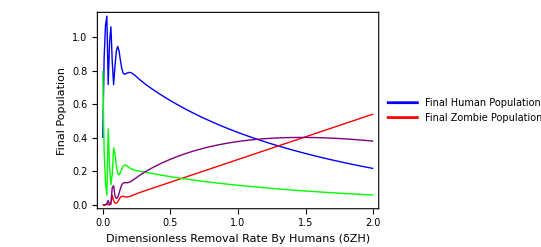

```mathematica
(* Compute final values of H and Z for varying deltaZ *)
finalValues = Table[
  Module[
    {sol, Hfunc, Zfunc, finalH, finalZ, Tfunc, Rfunc, finalT, finalR},
    (* Define the differential equations *)
    eqns = {
    H'[t] == - H[t] Z[t]+ βT T[t],
    Z'[t] == H[t] Z[t] - 1.36 T[t] Z[t] - 0.631 H[t] Z[t],
    T'[t] == 0.31 R[t] - βT T[t],
    R'[t] ==  0.631 H[t] Z[t] + 1.36 T[t] Z[t] - 0.31 R[t]
  };
    
    (* Solve the system numerically for the current deltaZ *)
    sol = NDSolve[
      {eqns, 
       H[0] == 500/500, 
       Z[0] == 50/500,
       T[0] == 50/500,
       R[0] == 0/500
      },
      {H, Z, T, R}, 
      {t, 0, 100}
    ];
    
    (* Extract the functions for H and Z *)
    Hfunc = H /. sol[[1]];
    Zfunc = Z /. sol[[1]];
    Tfunc = T /. sol[[1]];
    Rfunc = R /. sol[[1]];
    
    (* Extract the final values of H and Z at time tmax *)
    finalH = Hfunc[100];
    finalZ = Zfunc[100];
    finalT = Tfunc[100];
    finalR = Rfunc[100];
    
    (* Return the deltaZ and final values for plotting *)
    {βT, finalH, finalZ, finalT, finalR}
  ],
  {βT, 0, 2, 0.01} (* Vary deltaZ from 0 to 2 in steps of 0.01 *)
];

(* Separate deltaZ, H, and Z values for plotting *)
deltaZValues = finalValues[[All, 1]];
finalHValues = finalValues[[All, 2]];
finalZValues = finalValues[[All, 3]];
finalTValues = finalValues[[All, 4]];
finalRValues = finalValues[[All, 5]];

(* Plot final human and zombie populations as a function of deltaZ *)
ListLinePlot[
  {
   Transpose[{deltaZValues, finalHValues}],
   Transpose[{deltaZValues, finalZValues}],
   Transpose[{deltaZValues, finalTValues}],
   Transpose[{deltaZValues, finalRValues}]
  },
  PlotRange -> All,
  PlotLegends -> {"Final Human Population (H)", "Final Zombie Population (Z)"},
  PlotStyle -> {{Blue, Thick}, {Red, Thick}, {Green, Thick}, {Purple, Thick}},
  AxesLabel -> {"Zombie Removal Rate (δZ)", "Final Population"},
  Frame -> True,
  FrameLabel -> {"Dimensionless Removal Rate By Humans (δZH)", "Final Population"}
]
```

## Sensitivity To Initial Condition

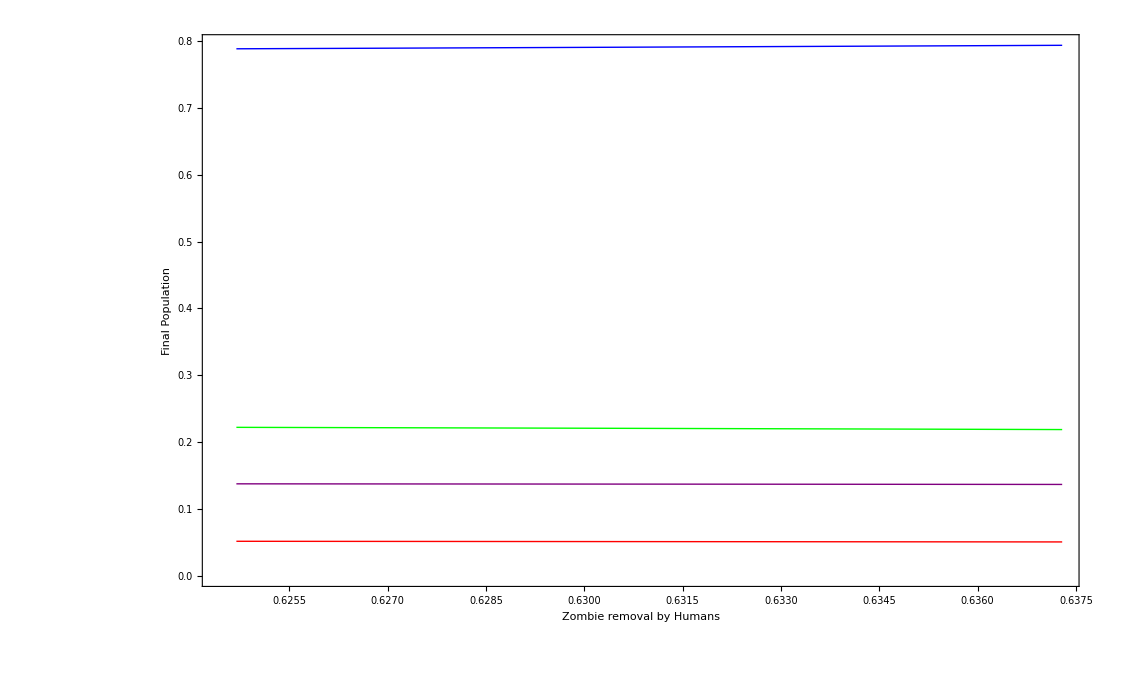

```mathematica
(* Compute final values of H and Z for varying deltaZ *)
finalValues = Table[
  Module[
    {sol, Hfunc, Zfunc, finalH, finalZ, Tfunc, Rfunc, finalT, finalR},
    (* Define the differential equations *)
    eqns = {
    H'[t] == - H[t] Z[t]+ 0.2 T[t],
    Z'[t] == H[t] Z[t] - 1.36 T[t] Z[t] - xX H[t] Z[t],
    T'[t] == 0.31 R[t] - 0.2 T[t],
    R'[t] ==  xX H[t] Z[t] + 1.36 T[t] Z[t] - 0.31 R[t]
  };
    
    (* Solve the system numerically for the current deltaZ *)
    sol = NDSolve[
      {eqns, 
       H[0] == 500/500, 
       Z[0] == 50/500,
       T[0] == 50/500,
       R[0] == 0/500
      },
      {H, Z, T, R}, 
      {t, 0, 100}
    ];
    
    (* Extract the functions for H and Z *)
    Hfunc = H /. sol[[1]];
    Zfunc = Z /. sol[[1]];
    Tfunc = T /. sol[[1]];
    Rfunc = R /. sol[[1]];
    
    (* Extract the final values of H and Z at time tmax *)
    finalH = Hfunc[100];
    finalZ = Zfunc[100];
    finalT = Tfunc[100];
    finalR = Rfunc[100];
    
    (* Return the deltaZ and final values for plotting *)
    {xX, finalH, finalZ, finalT, finalR}
  ],
  {xX, 0.62469, 0.63731, 0.0001} (* Vary deltaZ from 0 to 2 in steps of 0.01 *)
];

(* Separate deltaZ, H, and Z values for plotting *)
deltaZValues = finalValues[[All, 1]];
finalHValues = finalValues[[All, 2]];
finalZValues = finalValues[[All, 3]];
finalTValues = finalValues[[All, 4]];
finalRValues = finalValues[[All, 5]];

(* Plot final human and zombie populations as a function of deltaZ *)
ListLinePlot[
  {
   Transpose[{deltaZValues, finalHValues}],
   Transpose[{deltaZValues, finalZValues}],
   Transpose[{deltaZValues, finalTValues}],
   Transpose[{deltaZValues, finalRValues}]
  },
  PlotRange -> All,
  PlotStyle -> {{Blue, Thick}, {Red, Thick}, {Green, Thick}, {Purple, Thick}},
  Frame -> True,
  FrameLabel -> {"Zombie removal by Humans", "Final Population"}
]
```